```mathematica
ClearAll
```

ClearAll

```mathematica
Tensors = {6,8,9,11,12,15,16,19,20,24};
```

## System Matrices

### Final Matrices

```mathematica
FinalMatrices[Ntensors_]:=Module[{Ax,Ay,Shalf,ShalfInv,S,BC,result,var,varOdd,g,B,nEqn,varEven,varRearranged,PermuteMatrix,EntropyMat,Boe,OnsagerMat,Soe,PermuteMatInv,BCMat,filenameAx,filenameAy,filenameB,filenameOddID,percision,$MaxExtraPrecision=150,Bmbc},
result=GetMatrices2D[Ntensors];
BC=result⟦1⟧;
Ax = result⟦2⟧;
Ay = result⟦3⟧;
var = result⟦4⟧;
varOdd = result⟦5⟧;

(*no relaxational normal velocity*)
B = DevelopBNoRelax[BC,var,varOdd]⟦2⟧;
Bmbc = B;

S=GenerateSymmetrizer2D[Ntensors];
Shalf=MatrixPower[S,0.5];
ShalfInv=MatrixPower[S,-0.5];

nEqn=Length[Ax];

varEven = Delete[Range[1,nEqn],Map[{#}&,varOdd]];

(*Now we sort the variables considering an even and an odd splitting*)
varRearranged =Flatten[ConstantArray[0,{1,nEqn}]];
varRearranged⟦1;;Length[varOdd]⟧=var⟦varOdd⟧;
varRearranged⟦-Length[varEven];;-1⟧=var⟦varEven⟧;

PermuteMatrix = PermuteVar[var,varRearranged];
PermuteMatInv=PermuteVar[varRearranged,var];
EntropyMat = Transpose[PermuteMatrix].S.Ax.PermuteMatrix;
Soe = EntropyMat⟦1;;Length[varOdd],-Length[varEven];;-1⟧;

(*Permute B using even and odd splitting*)
B=B.PermuteMatrix;

(*Boundary Conditions of the form Uo=Boe*Ue. *)
Boe = -Inverse[B⟦1;;-1,1;;Length[varOdd]⟧].B⟦1;;-1,Length[varOdd]+1;;-1⟧;

(*We ignore the first boundary conditions and will deal with it later*)
OnsagerMat=ConstantArray[0,{Length[varOdd],Length[varOdd]}];
OnsagerMat=Simplify[Boe⟦1;;-1,1;;Length[Boe]⟧.Inverse[Soe⟦1;;-1,1;;Length[Soe]⟧]];

(*Now we fix the normal velocity by considering the first row of Soe to be the boundary condition for the normal velocity*)
OnsagerMat⟦1,1⟧=1;

(*Finally we have the new boundary conditions in the form Uo = Boe Ue*)
Boe=OnsagerMat.Soe;

(*From above we have the boundary conditions in the form Uo = Boe * Ue. Now we would like to change them into the form B.U=0. The first part into B will therefore be an Identity matrix and the second part will be -Boe*)
B⟦1;;-1,1;;Length[varOdd]⟧=IdentityMatrix[Length[varOdd]];
B⟦1;;-1,Length[varOdd]+1;;-1⟧=-Boe;

(*we now restore the original ordering of the variables through the matrix PermuteMatInv*)
B=B.PermuteMatInv;


{Ax,Ay,B,var,varOdd}

]
```

### Truncate matrices

```mathematica
CheckNullSpaceVariables[var_]:=Module[{result},

(*find the tensor degree of all the variables*)
result = Map[2#⟦1⟧+Total[#⟦2;;-1⟧]&,var];

(*substra*)
result=result/result⟦1⟧;

result = Length[Flatten[Position[result,1]]];

(*all the bad ones should be of the same tensor degree*)
If[result≠Length[var],Print[Style["Cannot Truncate the moment system",Red]];Abort[];];
]
```

```mathematica
(*if flag == 0, we get the old version, if flag == 1 we get the truncated one*)
TruncateMat[Ntensors_,flag_]:=Module[{Ax,Ay,B,var,varOdd,varEven,nEqn,numEven,numOdd,Perm,PermInv,varNew,result,posTrun,varOddNew,OddVar},

{Ax,Ay,B,var,varOdd} = FinalMatrices[Ntensors];

nEqn = Length[Ax];
varEven =Delete[Range[1,nEqn],Map[{#}&,varOdd]];
varEven =var⟦varEven⟧;
OddVar= var⟦varOdd⟧;

numEven = Length[varEven];
numOdd = Length[varOdd];

varNew= Flatten[{OddVar,varEven},1];

(*position of equal number of odd and evern variables*)
(*we check whether the null space is only coming from the higher order even moment or not.*)
CheckNullSpaceVariables[varNew⟦2*numOdd+1;;-1⟧];

posTrun = Flatten[ Position[var,Alternatives@@varNew⟦1;;2*numOdd⟧]];
varNew = var⟦posTrun⟧;

varOddNew=Flatten[Position[Map[If[OddQ[#⟦2⟧],1,0]&,varNew],1]];



(*Truncate matrices so as to obtain equal number of odd and even variables*)
Which[flag==0,
result={Ax,B,var,varOdd};
,flag==1,
result={Ax⟦posTrun,posTrun⟧,B⟦All,posTrun⟧,varNew,varOddNew};
];

result
]
```

# Solving Heat Conduction

## Return the Heat Conduction Variables

```mathematica
(*Given full set of variables, the following routine returns the variables involved in heat conduction.
These are those variables which have only an x-index. Since they are the ones which are involved in the heat conduction.*)
ReturnHeatVar[var_]:=Module[{result,pos},
result={};
pos={};

(*The assumption is that none of the variables contain the z-index. Therefore we only check for the y index. If the y index is zero then the variabls is involved in heat conduction*)
Do[If[var⟦ii⟧⟦3⟧==0,result=Join[result,{var⟦ii⟧}];pos=Join[pos,{{ii}}];];
,{ii,1,Length[var]}];

(*we also return the total number of variables involved in the heat conduction. The final result includes at first the variables involved in heat conduction and then the variables which were left out.*)
{Join[result,Delete[var,pos]],Length[pos]}
]
```

## Return the Matrix for Heat Conduction

```mathematica
MatrixHeat[Mat_,var_,varHeat_,numHeat_]:=Module[{Permute,PermuteInv,MatHeat},

Permute=PermuteVar[var,varHeat];
PermuteInv=PermuteVar[varHeat,var];

MatHeat=PermuteInv.Mat.Permute;

(*we first extract the matrix which plays a role in heat conduction*)
MatHeat=MatHeat⟦1;;numHeat,1;;numHeat⟧;

(*we now remove the rows corresponding to normal velocity and density. That means the upper block of 2 X 2 size*)
MatHeat=MatHeat⟦3;;-1,3;;-1⟧;

MatHeat
]
```

## Solving Routine(Core)

```mathematica
Clear[res,nn,var,eqn,B0,A0,P0,a,n,w,ww,unknowns,λ0,λ,λPlus,vv,v,Ansatz,Coefs,v0,v1,v2,v3,v4,C0,k,x,α,u]
GetSolutionHeat[Ntensors_,flag_,type_]:=Block[{res,nn,var,varC,eqn,b0,a,n,w,dw,λ0,λ,λPlus,v,vv,Ansatz,Coefs,C0,Signum,SymmetryConditions,k,x,jj,ii,Kn,α,numEqn,coef},

(*Delete is for removing the density and the velocity. The reason for removing the first equation is obvious. aIdx[[1]]+1 removes the energy balance because it contains the denstiy and the stress tensor. Since we are not interested in density, we let it go.*)


SystemData=TruncateMat[Ntensors,flag];
A0=MatrixHeat[SystemData⟦1⟧,SystemData⟦3⟧,ReturnHeatVar[SystemData⟦3⟧]⟦1⟧,ReturnHeatVar[SystemData⟦3⟧]⟦2⟧];
numEqn=Length[A0];

P0=SparseArray[{{i_,i_}->-1},numEqn];

(*only for energy balance, the momentum equation and the mass conservation has been ignored. *)
P0⟦1,1⟧=0;

(*generalized eigen vector and eigen value of P0 with respect to A0*)
{λ0,vv}=Chop[Eigensystem[{P0,1.0A0}]];

(*remove the zero and the infinite eigen values, why do the infinite eigen values appear? *)
λ=Select[λ0,(0<Abs[#]<∞)&];
v=Extract[vv,Flatten[Table[Position[λ0,item],{item,Select[λ0,(0<Abs[#]<∞)&]}],1]];

(*assumes symmetric spectrum and a certain ordering of the EV. First we have the negative ones and then the positive ones*)
λ=Flatten[Table[{Rationalize[λ⟦ii⟧,0],-Rationalize[λ⟦ii⟧,0]},{ii,1,Length[λ],2}]];

λPlus=Select[λ,(#>0)&];

If[type == 1,coef[0,3]=Kn k[0]];

(*a polynomial ansatz for homogeneous solution*)
Ansatz[x_]=Table[Sum[coef[jj,ii] x^jj,{jj,0,4}],{ii,1,numEqn}];
Coefs=Cases[Flatten[Table[Table[coef[jj,ii],{jj,0,4}],{ii,1,numEqn}]],coef[_,_]];

(*vector for the forcing term*)
B0=Table[0,{i,1,numEqn}];

(*only for poisson heat conduction we have the forcing*)
If[type==0,B0⟦1⟧=1];


(*ansatz for the particular solution of the equations.*)
Ansatz[x_]=Ansatz[x]/.Solve[Thread[Flatten[CoefficientList[A0.Ansatz'[x]-1/Kn P0.Ansatz[x]+α B0 x^2,x]]==0],Coefs]⟦1⟧/.{coef[_,_]->0};

Signum=Table[0,{ii,1,Length[λ],2}];

(*store the sign of the first non-zero entry in the eigenvectors*)

Do[jj=1;While[v⟦ii,jj⟧==0,jj++];Signum⟦(ii+1)/2⟧=-Sign[v⟦ii+1,jj⟧/v⟦ii,jj⟧],{ii,1,Length[λ],2}];

If[type==0,SymmetryConditions=Table[k[ii]->-Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}],SymmetryConditions=Table[k[ii]->Signum⟦(ii+1)/2⟧k[ii+1],{ii,1,Length[λ],2}]];

(*The final result is the particular solution + the solution to the homogeneous problem. The particular solution is the Ansatz and the homogeneous solution is the part: C0 B0+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn]*)

res=Chop[ExpToTrig[C0 B0+Ansatz[x]+Sum[k[ii] v⟦ii⟧Exp[λ⟦ii⟧x/Kn],{ii,1,Length[λ]}]/.SymmetryConditions/.Table[k[ii]->k[ii/2],{ii,1,Length[λ]}]]]/.Table[k[ii]->k[ii]Exp[-λPlus⟦ii⟧(1/2)/Kn],{ii,1,Length[λPlus]}]


];
```

```mathematica
u[x_]=GetSolutionHeat[11,1,1];

Chop[Expand[N[A0.u'[x]-1/Kn P0.u[x]+α B0 x^2]]]
```

{0,0,0,0,0,0,0,0}

## Boundary Conditions

```mathematica
GetBoundaryHeat[B_,var_,varOdd_]:=Module[{result,PermuteMat,varHeat,Bheat,PermuteMatOdd,varHeatOdd,numVarHeat,numVarHeatOdd,Brhs},


{varHeat,numVarHeat}=ReturnHeatVar[var];
{varHeatOdd,numVarHeatOdd}=ReturnHeatVar[var⟦varOdd⟧];

PermuteMat=PermuteVar[var,varHeat];
PermuteMatOdd=PermuteVar[varHeatOdd,var⟦varOdd⟧];

(*Ignoring the boundary condition from vx and the contribution from ρ and vx. Originally the boundary conditions are of the form Bu = g. Where u contains all the variables. So we first multiply from the left by the permutation matrix so that we collect the odd variables of the heat conduction problem. Then we multiply from the right so that we collect at the variables for the heat conduction problem. *)
Bheat=FullSimplify[PermuteMatOdd.B.PermuteMat]⟦2;;numVarHeatOdd,3;;numVarHeat⟧;
Brhs=-√(3/2)Bheat⟦All,1⟧thetaW;
(*We return the boundary in the form B.u+g*)
Bheat.varHeat⟦3;;numVarHeat⟧-Brhs
]
```

## Solving Procedure

```mathematica
(*flag == 0 for Original system and flag == 1 for TG. type==0 means poisson heat conduction*)
GetHeatConduction[kn_,θw_,alpha_,Ntensors_,flag_,type_]:=Module[{varHeat,numVarHeat,U,BC,BCrhs,BCmatrix,bcSol},

U=GetSolutionHeat[Ntensors,flag,type];

(*we first collect all the variables*)
(*The value of SystemData is prescribed inside the GetSolutionHeat*)
{varHeat,numVarHeat}=ReturnHeatVar[SystemData⟦3⟧];

(*we now remove density and velocity from the set of variables*)
varHeat=varHeat⟦3;;numVarHeat⟧;

BC=GetBoundaryHeat[SystemData⟦2⟧,SystemData⟦3⟧,SystemData⟦4⟧];

If[type == 0,{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[varHeat⟦ii⟧->U⟦ii⟧/.{x->1/2},{ii,1,Length[varHeat]}]/.{χ1->1,Kn->kn,α->alpha}),Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]];,{BCrhs,BCmatrix}=CoefficientArrays[(BC/.Table[varHeat⟦ii⟧->U⟦ii⟧/.{x->1/2},{ii,1,Length[varHeat]}]/.{χ1->1,Kn->kn,α->alpha}),Table[k[ii],{ii,0,Length[BC]-1}]];];

If[type==0,
bcSol=Thread[Join[{C0},Table[k[ii],{ii,1,Length[BC]-1}]]->Chop[-Inverse[BCmatrix].BCrhs]];,bcSol=Thread[Table[k[ii],{ii,0,Length[BC]-1}]->Chop[-Inverse[BCmatrix].BCrhs]];];


{Expand[U/.bcSol/.thetaW->θw/.α->alpha/.Kn->kn],varHeat}
]
```

```mathematica
{factθ,factσ,factq}={-√(2/3),√2,-√(5/2)};
{IDθ,IDσ,IDq}={1,2,-3};
```

# Reference Solution

### Poisson Heat

```mathematica
exactKn0p1 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactKn0p3 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactKn0p5 = Import["refs/Archive/BGKPoiseuilleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
exactKn0p1⟦All,4⟧+=1;
exactKn0p3⟦All,4⟧+=1;
exactKn0p5⟦All,4⟧+=1;

θExactKn0p1=Interpolation[exactKn0p1⟦All,{1,4}⟧];
σExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,6}⟧];
qExactKn0p1 = Interpolation[exactKn0p1⟦All,{1,7}⟧];

θExactKn0p3=Interpolation[exactKn0p3⟦All,{1,4}⟧];
σExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,6}⟧];
qExactKn0p3 = Interpolation[exactKn0p3⟦All,{1,7}⟧];

θExactKn0p5=Interpolation[exactKn0p5⟦All,{1,4}⟧];
σExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,6}⟧];
qExactKn0p5 = Interpolation[exactKn0p5⟦All,{1,7}⟧];
```

```mathematica
θExactKn0p3[x]
```

InterpolatingFunction[{{-0.5, 0.5}}, <>][x]

### Heat Conduction

```mathematica
exactHCKn0p1 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p1_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p3 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p3_nst600_Nc300_cMax5p0.dat"];

exactHCKn0p5 = Import["refs/Archive/BGKSimpleHeat/Result_BGKreduced_tau0p5_nst600_Nc300_cMax5p0.dat"];

(*fix for the wall temperature*)
(*exactHCKn0p1⟦All,4⟧+=1;
exactHCKn0p3⟦All,4⟧+=1;
exactHCKn0p5⟦All,4⟧+=1;*)

θExactHCKn0p1=Interpolation[exactHCKn0p1⟦All,{1,4}⟧];
σExactHCKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,6}⟧];
qExacHCtKn0p1 = Interpolation[exactHCKn0p1⟦All,{1,7}⟧];

θExactHCKn0p3=Interpolation[exactHCKn0p3⟦All,{1,4}⟧];
σExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,6}⟧];
qExactHCKn0p3 = Interpolation[exactHCKn0p3⟦All,{1,7}⟧];

θExactHCKn0p5=Interpolation[exactHCKn0p5⟦All,{1,4}⟧];
σExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,6}⟧];
qExactHCKn0p5 = Interpolation[exactHCKn0p5⟦All,{1,7}⟧];
```

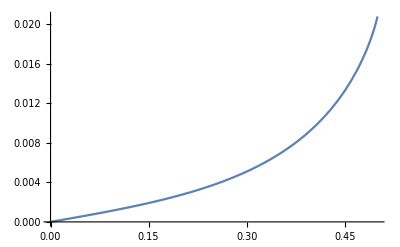

```mathematica
Plot[σExactHCKn0p1[x],{x,0,0.5}]
```

# Results (Poisson Heat Conduction)

### compute L2 error

```mathematica
ComputeL2Norm[data_]:=√2 Sqrt[NIntegrate[(data)^2,{x,0,0.5}]];

ComputeL2Error[Exact_,Num_]:=√2 Sqrt[NIntegrate[(Exact-Num)^2,{x,0,0.5}]];

ComputeErrorEntropy[Exact_,Num_,MomExact_,MomNum_]:=Module[{integrant,entries,varExact,varNum},


(*the difference in the entropy*)
integrant=Total[Flatten[{(Exact⟦1;;Length[Num]⟧-Num)(Exact⟦1;;Length[Num]⟧-Num),(Exact⟦Length[Num]+1;;-1⟧)(Exact⟦Length[Num]+1;;-1⟧)}]];

√2 Sqrt[NIntegrate[integrant,{x,0,0.5}]]];
```

### All theories

#### Kn 0.1

```mathematica
Kn = 0.1;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 0.3

```mathematica
Kn = 0.3;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 0.5

```mathematica
Kn = 0.5;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn0p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn0p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 1.5

```mathematica
Kn = 1.5;
θW=1.0;
α=√(2/3);
problemType = 0;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solKn1p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldKn1p5[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

#### error computation (Converge macroscopic quantities)

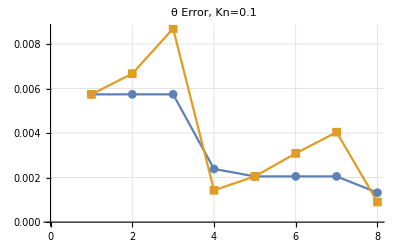

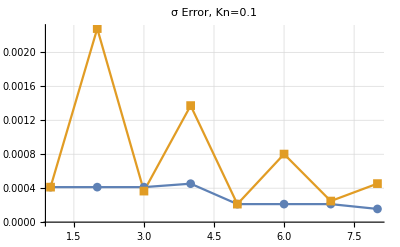

```mathematica
{errorTempKn0p1,errorStressKn0p1} = {Table[ComputeL2Error[θExactKn0p1[x],solKn0p1[ii][x]⟦IDθ⟧*factθ],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p1[x],solKn0p1[ii][x]⟦IDσ⟧*factσ],{ii,Tensors}]};

{errorTempOldKn0p1,errorStressOldKn0p1} = {Table[ComputeL2Error[θExactKn0p1[x],solOldKn0p1[ii][x]⟦IDθ⟧*factθ],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p1[x],solOldKn0p1[ii][x]⟦IDσ⟧*factσ],{ii,Tensors}]};


ListPlot[{errorTempKn0p1,errorTempOldKn0p1},Joined->True,GridLines->Automatic,PlotLabel->"θ Error, Kn=0.1",PlotMarkers->Automatic]


ListPlot[{errorStressKn0p1,errorStressOldKn0p1},Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.1",PlotMarkers->Automatic,PlotRange->Full]
```

```mathematica
{errorTempKn0p3,errorStressKn0p3} = {Table[ComputeL2Error[θExactKn0p3,temperatureKn0p3[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p3,stressKn0p3[ii]],{ii,Tensors}]};
```

```mathematica
{errorTempOldKn0p3,errorStressOldKn0p3} = {Table[ComputeL2Error[θExactKn0p3,temperatureOldKn0p3[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p3,stressOldKn0p3[ii]],{ii,Tensors}]};
```

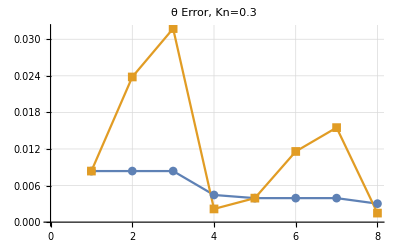

```mathematica
ListPlot[{errorTempKn0p3,errorTempOldKn0p3},Joined->True,GridLines->Automatic,PlotLabel->"θ Error, Kn=0.3",PlotMarkers->Automatic]
```

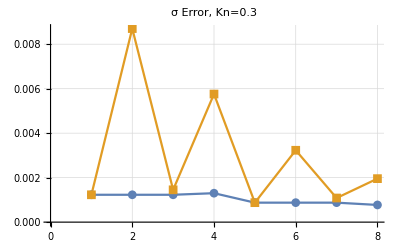

```mathematica
ListPlot[{errorStressKn0p3,errorStressOldKn0p3},Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.3",PlotMarkers->Automatic]
```

```mathematica
{errorTempKn0p5,errorStressKn0p5} = {Table[ComputeL2Error[θExactKn0p5,temperatureKn0p5[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p5,stressKn0p5[ii]],{ii,Tensors}]};
```

```mathematica
{errorTempOldKn0p5,errorStressOldKn0p5} = {Table[ComputeL2Error[θExactKn0p5,temperatureOldKn0p5[ii]],{ii,Tensors}],Table[ComputeL2Error[σExactKn0p5,stressOldKn0p5[ii]],{ii,Tensors}]};
```

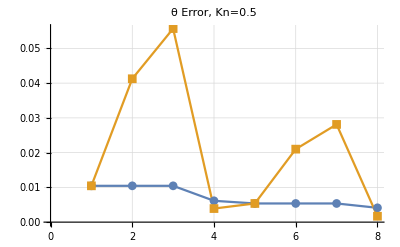

```mathematica
ListPlot[{errorTempKn0p5,errorTempOldKn0p5},Joined->True,GridLines->Automatic,PlotLabel->"θ Error, Kn=0.5",PlotMarkers->Automatic]
```

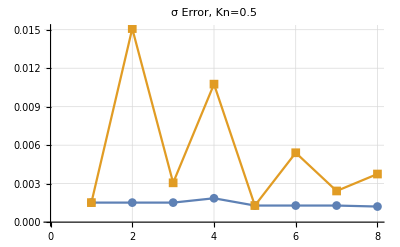

```mathematica
ListPlot[{errorStressKn0p5,errorStressOldKn0p5},Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.5",PlotMarkers->Automatic]
```

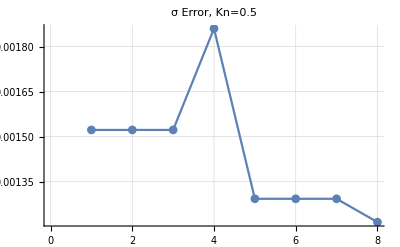

```mathematica
ListPlot[errorStressKn0p5,Joined->True,GridLines->Automatic,PlotLabel->"σ Error, Kn=0.5",PlotMarkers->Automatic]
```

#### error computation (Converge Entropy)

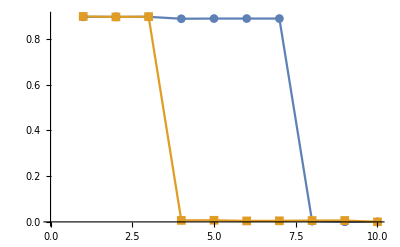

```mathematica
errorEntropyKn0p1 = Quiet[Table[ComputeErrorEntropy[solKn0p1[Tensors⟦-1⟧][x],solKn0p1[ii][x]],{ii,Tensors}]];

errorEntropyOldKn0p1 = Quiet[Table[ComputeErrorEntropy[solOldKn0p1[Tensors⟦-1⟧][x],solOldKn0p1[ii][x]],{ii,Tensors}]];

ListPlot[{errorEntropyKn0p1,errorEntropyOldKn0p1},Joined->True,PlotMarkers->Automatic]
```

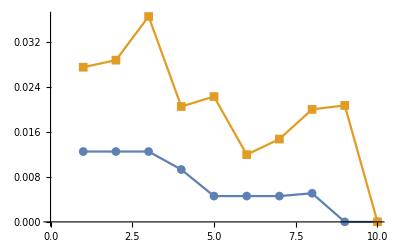

```mathematica
errorEntropyKn0p3 = Quiet[Table[ComputeErrorEntropy[solKn0p3[Tensors⟦-1⟧][x],solKn0p3[ii][x]],{ii,Tensors}]];

errorEntropyOldKn0p3 = Quiet[Table[ComputeErrorEntropy[solOldKn0p3[Tensors⟦-1⟧][x],solOldKn0p3[ii][x]],{ii,Tensors}]];
ListPlot[{errorEntropyKn0p3,errorEntropyOldKn0p3},Joined->True,PlotMarkers->Automatic]
```

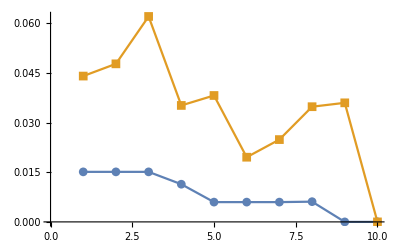

```mathematica
errorEntropyKn0p5 = Quiet[Table[ComputeErrorEntropy[solKn0p5[Tensors⟦-1⟧][x],solKn0p5[ii][x]],{ii,Tensors}]];

errorEntropyOldKn0p5 = Quiet[Table[ComputeErrorEntropy[solOldKn0p5[Tensors⟦-1⟧][x],solOldKn0p5[ii][x]],{ii,Tensors}]];
ListPlot[{errorEntropyKn0p5,errorEntropyOldKn0p5},Joined->True,PlotMarkers->Automatic]
```

# Results (Heat Conduction)

### Sequence of convergence

#### Kn 0.1

```mathematica
Kn = 0.1;
θW=1.0;
α=0;

problemType = 1;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solHCKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldHCKn0p1[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### Kn 0.3

```mathematica
Kn = 0.3;
θW=1.0;
α=0;

problemType = 1;
systemType = 1;

Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solHCKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];

systemType = 0;
Do[Print[Style["Num Tensors: ",FontColor->Magenta],ii];
solOldHCKn0p3[ii][x_]=GetHeatConduction[Kn,θW,α,ii,systemType,problemType];,{ii,Tensors}];
```

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

Num Tensors: 6

Num Tensors: 8

Num Tensors: 9

Num Tensors: 11

Num Tensors: 12

Num Tensors: 15

Num Tensors: 16

Num Tensors: 19

Num Tensors: 20

Num Tensors: 24

#### error computation (Converge Entropy)

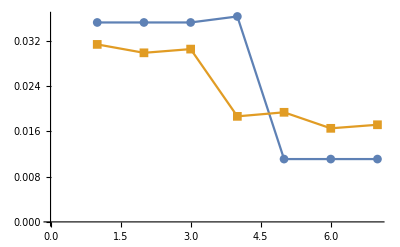

```mathematica
errorEntropyHCKn0p1 = Quiet[Table[ComputeErrorEntropy[solHCKn0p1[Tensors⟦-1⟧][x],solHCKn0p1[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

errorEntropyOldHCKn0p1 = Quiet[Table[ComputeErrorEntropy[solOldHCKn0p1[Tensors⟦-1⟧][x],solOldHCKn0p1[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

ListPlot[{errorEntropyHCKn0p1,errorEntropyOldHCKn0p1},Joined->True,PlotMarkers->Automatic]
```

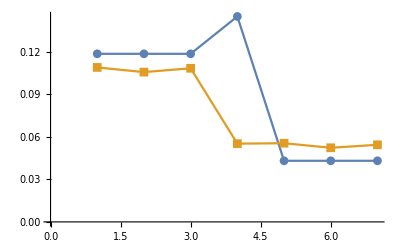

```mathematica
errorEntropyHCKn0p3 = Quiet[Table[ComputeErrorEntropy[solHCKn0p3[Tensors⟦-1⟧][x],solHCKn0p3[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

errorEntropyOldHCKn0p3 = Quiet[Table[ComputeErrorEntropy[solOldHCKn0p3[Tensors⟦-1⟧][x],solOldHCKn0p3[ii][x]],{ii,Tensors⟦1;;-4⟧}]];

ListPlot[{errorEntropyHCKn0p3,errorEntropyOldHCKn0p3},Joined->True,PlotMarkers->Automatic]
```